# Bistable motif: 2kinase1substrate

## Finding the condition of multistationarity

We consider the following reactions:

K+S→KS→K+S_p
K_p+S→K_p S→K_p+S_p
K→K_p
KS←K_p S
E+S→ES→E+S_p
E_p+S→E_p S→E_p+S_p
E→E_p
ES←E_p S
S_p→S

The species of the system are:

{S,S_p,K,K_p,KS,K_p S,E,E_p,ES,E_p S}

In total, there are 13 reations and 10 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{13},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;
A[[2]][[3]]=1;A[[2]][[2]]=1;A[[2]][[5]]=-1;
A[[3]][[1]]=-1;A[[3]][[4]]=-1;A[[3]][[6]]=1;
A[[4]][[4]]=1;A[[4]][[2]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[4]]=1;A[[6]][[5]]=1;A[[6]][[6]]=-1;
A[[13]][[2]]=-1;A[[13]][[1]]=1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[9]]=1;
A[[8]][[7]]=1;A[[8]][[2]]=1;A[[8]][[9]]=-1;
A[[9]][[1]]=-1;A[[9]][[8]]=-1;A[[9]][[10]]=1;
A[[10]][[8]]=1;A[[10]][[2]]=1;A[[10]][[10]]=-1;
A[[11]][[7]]=-1;A[[11]][[8]]=1;
A[[12]][[9]]=1;A[[12]][[10]]=-1;
```

```mathematica
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,1,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 4]×Subscript[x, 6],Subscript[k, 5]×Subscript[x, 3],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 7]×Subscript[x, 1],Subscript[k, 8]×Subscript[x, 9],Subscript[k, 9]×Subscript[x, 8]*Subscript[x, 1],Subscript[k, 10]*Subscript[x, 10],Subscript[k, 11]*Subscript[x, 7],Subscript[k, 12]×Subscript[x, 10],Subscript[k, 13]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_5,k_3 x_1 x_4,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_9,k_9 x_1 x_8,k_10 x_10,k_11 x_7,k_12 x_10,k_13 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_13 x_2-k_1 x_1 x_3-k_3 x_1 x_4-k_7 x_1 x_7-k_9 x_1 x_8,-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_5,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,-k_11 x_7-k_7 x_1 x_7+k_8 x_9,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,k_9 x_1 x_8-k_10 x_10-k_12 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,0,1,1,0,0,1,1},{0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2],Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 3]};
```

```mathematica
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],ssEqns[[8]],ssEqns[[9]],cons[[1]],cons[[2]],cons[[3]]}
```

{-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,-T_1+x_1+x_2+x_5+x_6+x_9+x_10,-T_2+x_3+x_4+x_5+x_6,-T_3+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[{ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{{x_3→(k_2 k_3 k_6 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_4→(k_2 k_5 (k_4+k_6) T_2)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_5→(k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_6→(k_2 k_3 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)}}

```mathematica
sol2=Solve[{ssEqns[[8]],ssEqns[[9]],ssEqns[[10]],cons[[3]]}==0,{Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_7→(k_8 k_9 k_12 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_8→(k_8 k_11 (k_10+k_12) T_3)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_9→(k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_10→(k_8 k_9 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)}}

```mathematica
sol3=Subscript[x, 2]/.Solve[{ssEqns[[2]]==0},{Subscript[x, 2]}]
```

{(k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10)/k_13}

```mathematica
sol4=Solve[{Subscript[x, 2]==sol3[[1]]}/.Join[sol1[[1]],sol2[[1]]],{Subscript[x, 2]}]
```

{{x_2→1/k_13((k_2 k_3 k_4 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_2 k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_8 k_9 k_10 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_8 k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2))}}

```mathematica
term=FullSimplify[Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1]/.Join[sol1[[1]],sol2[[1]],sol4[[1]]]]
```

-T_1+(x_1 ((k_3 T_2 (k_5 (k_6 k_13+k_2 (k_4+k_6+k_13))+k_1 k_6 (k_2+k_13) x_1))/(k_3 k_6 x_1 (k_5+k_1 x_1)+k_2 (k_5 (k_4+k_6)+k_3 (k_5+k_6) x_1))+(k_9 k_12 k_13 (T_3+x_1) (k_11+k_7 x_1)+k_8 (k_11 ((k_10+k_12) k_13+k_9 (k_10+k_12+k_13) T_3)+k_9 ((k_11+k_12) k_13+k_7 k_12 T_3) x_1))/(k_9 k_12 x_1 (k_11+k_7 x_1)+k_8 (k_11 (k_10+k_12)+k_9 (k_11+k_12) x_1))))/k_13

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_11 k_12 k_13 T_1+(k_2 k_4 k_5 k_8 k_10 k_11 k_13+k_2 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_11 k_12 k_13+k_2 k_5 k_6 k_8 k_11 k_12 k_13-k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_10 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13+k_2 k_5 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_8 k_10 k_11 k_13+k_2 k_3 k_6 k_8 k_10 k_11 k_13+k_3 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_11 k_12 k_13+k_2 k_3 k_6 k_8 k_11 k_12 k_13+k_3 k_5 k_6 k_8 k_11 k_12 k_13+k_2 k_4 k_5 k_9 k_11 k_12 k_13+k_2 k_5 k_6 k_9 k_11 k_12 k_13-k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_9 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_11 T_2+k_1 k_2 k_3 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_4 k_5 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_2+k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_3 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_3+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1^2+(k_2 k_3 k_5 k_8 k_9 k_11 k_13+k_2 k_3 k_6 k_8 k_9 k_11 k_13+k_3 k_5 k_6 k_8 k_9 k_11 k_13+k_1 k_3 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_7 k_9 k_12 k_13+k_2 k_5 k_6 k_7 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_9 k_12 k_13+k_2 k_3 k_6 k_8 k_9 k_12 k_13+k_3 k_5 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_11 k_12 k_13+k_2 k_3 k_5 k_9 k_11 k_12 k_13+k_2 k_3 k_6 k_9 k_11 k_12 k_13+k_3 k_5 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_8 k_9 k_11 T_2+k_2 k_3 k_4 k_5 k_7 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_7 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_9 k_11 k_12 T_2+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_2+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_3 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_3+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_3) x_1^3+(k_1 k_3 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_7 k_9 k_12 k_13+k_2 k_3 k_6 k_7 k_9 k_12 k_13+k_3 k_5 k_6 k_7 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_7 k_9 k_12 T_2+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_3) x_1^4+k_1 k_3 k_6 k_7 k_9 k_12 k_13 x_1^5

This is a degree 5 polynomial which presumably admits 5 positive real roots. Any real root of this polynomial leads to a steady state for the fixed rate constants and total amounts. The values of the other variables at steady states are found by plugging the value of x1 (the root of the polynomial) into the expressions in sol1, sol2, and sol3 above.

A necessary condition for 5 positive roots is that the signs of the coefficient of the polynomial (in x1) alternate.
This is a pre-check when you do the sampling: you need to impose the coefficient of x1^4 to be  negative , the coefficient of x1^3 to be positive, the coefficient of x1^2 to be  negative and the coefficient of x1 to be positive. The coefficients of x1^5 and the independent term always have the right sign.

## Sampling the parameters to make the term has 5 roots

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^3+(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]^5;
```

#### Coeffs

```mathematica
coeff1=Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3];
coeff2=(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff3=(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff4=(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
```

#### Sampling

```mathematica
ss2ParSets={};
ss2PolSets={};
ss2SolSets={};
ss3ParSets={};
ss3PolSets={};
ss3SolSets={};
ss4ParSets={};
ss4PolSets={};
ss4SolSets={};
ss5ParSets={};
ss5PolSets={};
ss5SolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]];
tots=Exp[RandomReal[{Log[0.001],Log[1000.]},3]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
Switch[Length[Flatten[solution]],2,{
AppendTo[ss2ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss2PolSets,pol/.subs];
AppendTo[ss2SolSets,Flatten[solution]];
biCount++;},3,{
AppendTo[ss3ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss3PolSets,pol/.subs];
AppendTo[ss3SolSets,Flatten[solution]];
multiCount++;},4,{
AppendTo[ss4ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss4PolSets,pol/.subs];
AppendTo[ss4SolSets,Flatten[solution]];
multiCount++;},5,{
AppendTo[ss5ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss5PolSets,pol/.subs];
AppendTo[ss5SolSets,Flatten[solution]];
multiCount++;}
];
(*}];*)
},{i,5000000}];
]
```

{15675.3,Null}

```mathematica
Length[ss2ParSets]
```

40267

```mathematica
Length[ss3ParSets]
```

6513

```mathematica
Length[ss4ParSets]
```

135

```mathematica
Length[ss5ParSets]
```

4

```mathematica
InputForm[ss5ParSets]
```

{{30.26907055950005, 0.015345031904046718, 379.2818135708148, 3.8082251354658188, 0.0036687528444848427, 
 0.13296589686376084, 310.1595399836181, 0.021043418057000815, 0.016491372377285016, 39.76104156980563, 9.061356696657525, 
 0.023576257909081366, 0.0023689836151906487, 845.7868156657265, 57.56286728182886, 16.45292963069698}, {12.791536262377333, 
 0.0034898324955981988, 124.48490665956912, 14.364956625123318, 1.8820643829200225, 0.06207039508084975, 5.36634369662495, 
 0.1395233965784267, 6.127307127467282, 348.2943196285812, 0.6139560154556575, 0.004203521315153397, 0.006595294405600259, 
 431.8992457693107, 12.136890753339557, 0.18502617556413403}, {5.879137085516735, 0.0033751979024755916, 2.107719796978838, 
 500.69023689470674, 0.037972916416413455, 48.025982227857675, 67.40947817881231, 0.004277486460006026, 0.16410793866624665, 
 30.195763275878235, 0.4278526927277934, 0.002727157259805876, 0.0015127395140503617, 829.7331212580159, 110.97744997193716, 
 25.07248294701992}, {0.03863067640002412, 0.06964020400731227, 12.893107874913023, 717.0141199745967, 0.016845994678178475, 
 0.001941863314613148, 0.515261967967496, 0.0011924697492939357, 58.62046075778042, 242.79254583735883, 
 0.0018562783780476306, 4.143110610314261, 0.0034828788856501665, 980.5678137212656, 0.02294111016031769, 
 200.56979547299036}}

```mathematica
InputForm[ss5SolSets]
```

{{0.0001673179574018385, 0.0017701734788143613, 4.211495208850604, 28.136233827022362, 220.35377804688864}, 
 {0.0026993292596905116, 0.5143459784462802, 1.8447433928056391, 126.15341072811653, 276.6322493206081}, 
 {0.011201423386435755, 0.024705675213822165, 0.13170436103981822, 13.63860745022466, 361.34661097799966}, 
 {0.00045859801424694336, 0.013160505343201727, 11.37445257762346, 92.04118330552284, 589.5323347053119}}

```mathematica
InputForm[ss4ParSets]
```

{{25.188551503179244, 0.00204695898805143, 1.9727911780209786, 11.755781988841745, 0.07245672799508228, 0.01725916863769819, 
 287.8435659919772, 0.013527281469719215, 5.443863731792746, 297.9958439087453, 333.74878226961107, 2.1873460984477613, 
 0.08075520225119703, 228.60733527535828, 45.34000816922439, 21.760214729298454}, {58.497772850912895, 
 0.0038603408444063568, 11.498460022528475, 79.12639768356617, 11.605571520586379, 0.004682173957753381, 1.6864085022586421, 
 0.01717889548561475, 37.47663381114181, 125.60541930880233, 0.004842051976227469, 0.05093438420043178, 
 0.022081431417385743, 462.9533493755681, 10.78626281094238, 1.910048245346067}, {0.4798762424672489, 0.016589740511139813, 
 0.007469832158748138, 80.45884347510967, 11.326186889439857, 0.0028037076635538806, 5.194152081498388, 0.18542772764789434, 
 191.31871056354208, 4.15392306598246, 16.174511565615866, 0.014231431598754053, 0.010889671689535314, 812.949569776478, 
 0.6584628691382377, 4.446435938231032}, {12.480415117517381, 0.07120718817478072, 125.1945911409097, 96.52155903812226, 
 0.028938432364338948, 0.015108686820174463, 9.686929869047255, 0.2385224884439584, 0.05995575264389427, 53.669780672420835, 
 0.03568042251235294, 0.03856607719550489, 0.005229744594075047, 415.21710512340826, 11.323411527594402, 
 0.2889068506820578}, {291.03240659966315, 0.2342949067569108, 711.6329768393709, 80.26630217083756, 0.12480747478651641, 
 0.08618478513224369, 0.3924311799934217, 0.002390056447211753, 0.052736464665423956, 67.46565877367044, 
 0.001069255821605476, 0.0015754794052454957, 0.03046619951251487, 12.54948740034782, 0.4089064271570779, 
 0.10699349625737498}, {1.9492238958710262, 0.009300591255723823, 0.047995835912617336, 58.53684624460959, 
 0.020833668856692574, 0.0070206677646165415, 303.074002185963, 2.502573736983759, 11.560138985795264, 146.83320347529184, 
 0.7450701831706353, 0.055775732316986584, 2.1685532400173297, 95.3870232052112, 1.2455745719021358, 28.059557256177342}, 
 {2.0037828041766357, 0.03402521016745339, 5.658733664556888, 513.0671087441602, 0.46554662823766, 0.06607915599307337, 
 3.7059598422699884, 0.04867750032165441, 0.0035428976864038896, 2.999426512740749, 0.6774977040706005, 
 0.020136262948815375, 0.010659989400185954, 298.06819940289324, 0.589088612974441, 2.9171042291547096}, 
 {193.57715052912212, 0.03575330973241055, 0.010981458156951757, 0.16715170852818634, 25.223490914402387, 
 0.002957361361992875, 104.76782314334778, 0.001859059165290921, 74.20510718219381, 656.267150140365, 0.03349723999518873, 
 42.10963848996843, 0.0020329575497079534, 889.4579572130219, 15.174023120976619, 167.37325316927448}, {14.202522272551697, 
 0.0670671941608537, 298.863568976553, 75.76271891701637, 4.769752288622317, 0.02009431662859119, 928.6821709089654, 
 1.092448171062527, 0.008101836115753118, 10.185809699850129, 9.165161369328713, 0.10597508995715399, 0.01077407172334992, 
 695.9841126672602, 0.8648475650688308, 1.5042677608639958}, {2.8476314308674415, 0.00462223589319534, 264.1019654740766, 
 5.181849695545819, 0.003805499413521499, 0.001347544733511051, 21.043316747007086, 0.03596238278318307, 1.7695677672115266, 
 299.9710205904382, 9.393762093908986, 0.008193382240823726, 0.3257817308121131, 797.7803924126001, 263.3121176558222, 
 386.9366034874348}, {68.55235360722247, 0.01577142940125249, 176.29628537615562, 91.08028520977473, 44.049283912171916, 
 0.15166017424466835, 0.045369292450525164, 0.012634319292359347, 0.009381766881164351, 16.54450661666596, 
 0.025822357715099883, 0.0035269112397481985, 0.03211730728643748, 614.2007217882425, 5.762974560039818, 262.9054758927001}, 
 {410.5500621386464, 0.016181984881410864, 0.0034570390468447155, 0.5592114933242484, 0.3521233610792501, 500.2691145469413, 
 376.03171352675923, 0.07232084084596214, 707.9148171157786, 398.5885145860232, 0.8760649797345879, 9.05383022292051, 
 0.1291353019117233, 2.9183583718407307, 0.1943958574984222, 1.0253697937279107}, {0.022768103579043148, 
 0.09843355721486635, 0.08616285694042893, 1.3239194916658932, 0.006013092121336691, 0.016836255754844175, 
 2.498991058998353, 0.0038708475433098543, 645.3397809711122, 135.2314546010471, 0.31386808680308137, 0.0035473054901640536, 
 0.01772542403723327, 29.088853395458642, 2.2573577458587217, 0.02245833396761264}, {45.89356988554017, 
 0.002103873543061958, 0.10133048230214044, 489.86465770563376, 6.347872917087362, 15.14782892638982, 15.907084932688575, 
 0.0018213869182455013, 0.10734637339306298, 76.63167038655993, 0.08000811715963567, 13.536656325840074, 
 0.0015075812806123097, 171.41220961239296, 16.482368795927318, 44.349261118734006}, {1.5777094167688286, 
 0.00382111429589172, 717.9158641654134, 1.9219865184116898, 0.0027008586328960346, 0.006423282178847995, 29.3304513669427, 
 0.6899880608568036, 14.717265977975826, 248.31444145717487, 2.762869145033419, 4.415613308055474, 0.004812182510574281, 
 110.7695415532577, 14.96662531492094, 0.2954792166735896}, {4.129383304611878, 0.014881085533436221, 0.13634061107432627, 
 5.771013903330811, 3.4866278221237845, 0.007551118987411439, 1.106092737025164, 0.09480558574411208, 90.8553350516375, 
 31.00347697150901, 0.12662745074867945, 0.00672671272599941, 0.008844692246426132, 394.1269302976841, 1.5263639525337414, 
 0.23347587803465703}, {0.02079765790053677, 0.005876551055850185, 0.019195128653702195, 24.576137066527615, 
 0.42084331330902514, 0.0038250918372289343, 0.15135036226795795, 0.0026167873601705693, 0.8011859568414026, 
 195.32067786072264, 0.5390263239116154, 3.9772827452751187, 0.004582356668358265, 596.4143380966191, 0.1975532919723275, 
 31.364502780096117}, {3.839267546392488, 0.30485139792253346, 670.8483011192727, 661.1361565980458, 0.05614962779276613, 
 0.003608084662777599, 36.62989250740341, 0.08679056115274425, 0.0021271219765917676, 35.82466279755554, 0.3418476983362897, 
 0.012813684541058473, 35.11278438438799, 331.2288423837199, 121.45114201867644, 115.8831890741551}, {142.3489955895014, 
 0.060769270265005115, 0.0020480767086507004, 1.0930192480124974, 57.570743556688285, 0.08685559560877369, 
 0.06846208816505422, 0.12149916552834776, 164.53368775664276, 362.7470388371392, 0.0022315024890209117, 
 0.001624448500785279, 0.02238757002445883, 35.95825621050234, 1.055351626824297, 0.007784068009036422}, 
 {2.1808488112567628, 0.17620928875481412, 0.011368367941938481, 19.20874217898993, 0.006931746835898123, 
 0.001191540618057581, 2.2853280319191684, 0.018375666366269135, 0.4996487303374753, 9.720428952610655, 0.2800849042750373, 
 0.15696549668145315, 0.00541662369611493, 52.17764262219156, 0.3773172543510509, 3.2743124616888806}, {44.9169305545805, 
 0.6564843031335552, 820.5615031487602, 3.42389598587601, 0.9236091237854119, 0.0946075714956352, 0.42722525556554575, 
 0.0012421597229855883, 0.004742059492936044, 964.3177578560475, 0.017466379943415676, 4.750957033817862, 
 2.8100887965855748, 183.1211376904734, 130.52744043888964, 18.797377092818177}, {8.229133228690738, 0.17447823398395465, 
 0.004415208080190799, 224.45722523353265, 0.12851495698065923, 10.426200851943609, 0.6445120942768595, 0.00554096958303903, 
 118.80154810871487, 449.44476122458957, 0.5137654599876053, 0.14804725424614987, 0.0016793237769932659, 123.38534111573719, 
 0.04234388452334653, 0.07091196314715806}, {0.6750177570061001, 0.015062719614089436, 0.011198135242136687, 
 254.8578044360998, 0.4583462971868125, 0.8834396464410681, 559.0071126319395, 2.083122676939482, 279.4626971249557, 
 94.27654146336886, 2.6996215013978424, 0.3882080864178131, 0.007829049075520737, 44.62442372755862, 0.5206599499826312, 
 0.037984410850876484}, {0.946953869456287, 0.0019326670165285267, 2.697280306097259, 299.8715753900161, 
 0.03288646565405989, 4.604833179445833, 585.2072477523884, 5.301001876837074, 0.016742231293411767, 2.3911084533814777, 
 0.014055086038158422, 1.2225537550401688, 0.003355192651579457, 459.8659099116824, 52.01489131694044, 0.07496450316192137}, 
 {105.23668445075924, 0.2808697630793229, 3.424615489567718, 642.5460203824019, 0.2885971423047, 0.0049909620600729785, 
 0.5594795328427941, 0.06736057817789139, 0.006742342465525781, 76.90943360537875, 0.0034095061609786975, 
 0.04298492607833669, 0.004661594098567381, 74.52211474463411, 0.047000389433531485, 0.3700489032828179}, 
 {2.2221174432802164, 0.00816369076367017, 6.57241727246759, 17.19367862184247, 0.2925058696020748, 0.01841034759054719, 
 106.58804836215089, 0.15438692179690688, 0.013802314054870306, 34.789717173800845, 0.22614444140525275, 
 0.001680926137397825, 0.001369769073028101, 65.18624205715797, 0.40093389242404814, 0.07998852106192332}, 
 {0.34707538597451787, 0.007174058349059929, 1.854987158907338, 25.51186626342505, 1.6502429523618776, 0.022337240586203636, 
 345.2206051980433, 0.09453668260722595, 713.3823598641648, 11.347357631988041, 28.991117780395555, 2.9652764245146956, 
 0.05392196689005209, 36.38235407099403, 0.6755143991074934, 4.8395029135028835}, {817.9424742897799, 0.5302551381410898, 
 59.742913107850946, 356.61360566741126, 0.3382093106105004, 0.006800694230743118, 99.8184285344835, 0.13631180263336973, 
 687.4106873094993, 1.5507566936857329, 0.006267853652082725, 0.00263317681280744, 0.004143637017486543, 375.7421325040427, 
 0.6264495102223968, 2.935078587609578}, {1.0228282977635288, 0.008112190557582225, 52.34399590208253, 578.9433904431021, 
 0.005871112065274234, 4.370421659016074, 79.55966754118829, 14.131020388602984, 12.905971183112257, 173.84110659776977, 
 78.51972737617554, 0.7324407416068937, 0.006544508330193408, 218.32592855050373, 18.964861772379138, 0.06269395172571089}, 
 {104.97339178506039, 0.008938372377745276, 144.81915088965394, 148.54421840564012, 21.745844377284126, 
 0.0011229522205839328, 0.6320518516243104, 0.0023796057501189686, 0.0030397592906148433, 349.97827362730516, 
 0.111942896328415, 0.0032847680566174342, 0.09402141945099828, 184.43132459853155, 0.8367253343858, 0.3464084606893949}, 
 {8.37567978283515, 0.03355541260613245, 0.0022738540534110946, 45.93174426224191, 0.1681405464182259, 0.1027654810316293, 
 0.09229152451783569, 0.0014253016502693702, 114.30084881026063, 665.9194896021222, 0.006871967388282023, 
 0.004241690035683005, 0.0014442095486292062, 16.42273647690755, 0.013554748184540895, 0.003313449319304406}, 
 {2.761927258786599, 0.004738393223331329, 0.048217434371867526, 16.996821378767617, 0.02242245338121906, 
 0.30760683355281515, 2.0929069791965724, 0.007128427929586548, 0.22533115512428203, 448.3801381623644, 
 0.031331327027049445, 0.26103865176227264, 0.003363172294903823, 16.60952665579111, 3.0730165085310417, 
 0.21265911048331188}, {660.4864838760411, 1.904113793550148, 0.2579841748153479, 8.237875268729852, 0.016031627226736664, 
 0.02547451492879226, 90.82378806854412, 0.35283816490425013, 607.9834633124811, 2.9101192470274, 32.48727125370648, 
 0.518881994117553, 0.6242553460100452, 3.8542921069044827, 0.05756092930974417, 1.2859282757932349}, {68.93825443671169, 
 0.009684540987178943, 0.023478646313359806, 906.0042786063447, 0.001638414639805731, 0.0029080750795329856, 
 19.95583476987096, 0.001316065213047041, 0.2367806385960112, 37.783110289753026, 0.039161681115127814, 
 0.0015190446622752932, 0.0015128258083271073, 454.47175493520683, 39.87976518752853, 7.222519246257297}, 
 {366.37368292041805, 0.003999425372025712, 2.189963789239749, 187.51721113408456, 44.6824895848078, 0.011261923512423966, 
 83.98559546376224, 0.019783340737189386, 2.6128805552212606, 314.57013895563216, 0.03283339412369674, 
 0.0063616495637398756, 0.002797653873167049, 221.55838400264764, 1.7032645288035553, 5.174043191279038}, 
 {1.3342911155204062, 0.3871368561544018, 153.79587742876126, 16.928263648682144, 0.32241332839727405, 0.53669771764679, 
 1.0556966059753292, 0.020201705457176856, 0.01803301536618399, 998.9528933735506, 0.3157112935713515, 5.362685172341907, 
 0.047802765916960185, 565.4530629194562, 14.00534976903726, 8.189141032863029}, {305.17550676959434, 1.3432140918779167, 
 0.007211174125996522, 1.1341815231021286, 0.8531321122258126, 4.15866459462369, 12.54957615909823, 0.002765730901622808, 
 37.273854713696736, 68.34274051858617, 0.19567300703352647, 0.0021321648698140886, 0.005432099527555607, 
 51.905490959580334, 0.023084904404974155, 0.252253720250657}, {0.049398071408337754, 0.040704803383179625, 
 935.4484323291941, 16.857848785699865, 0.14579997275591372, 0.5585531951747755, 0.09073365271465811, 0.043556207284417475, 
 0.06885445870556617, 130.536841778395, 7.5255287010916945, 0.7768906472570583, 0.053350987932934836, 277.2704944352755, 
 18.286161687491518, 3.2020804911139447}, {10.888878168739515, 0.0020943596076950007, 566.6007347531634, 36.018429829107454, 
 0.07849084166027696, 1.0329107794223154, 455.3793401967649, 0.0324655889413554, 0.013578413079622816, 2.4495288180891923, 
 0.345359176261558, 0.0014920825820175932, 0.0013822679454674465, 450.644159628762, 13.518782768823801, 10.923336161874714}, 
 {8.168283700261954, 0.0015373845852239435, 212.9037827938908, 998.5835829014829, 0.00248812507113296, 44.2972711436776, 
 0.2499548691652235, 0.0657898156256296, 0.18869092375524668, 3.8922793472104846, 0.023848820465344808, 0.01704452723523099, 
 0.0010565861618829387, 806.3189170661379, 208.84939738633133, 3.7175225089662844}, {11.030405097779079, 
 0.002684483015659531, 0.013533287338220856, 0.5595512074295034, 0.018047328721018798, 0.006688582608840827, 
 52.93532519788873, 0.001915154207530782, 190.08853655890948, 1.0212053377729209, 0.03546355967632722, 
 0.0014672409367695836, 0.0013546289433930526, 251.20696975485006, 5.6750713471902925, 3.536272001834639}, 
 {277.3633257414596, 0.009352144114522004, 9.390676380950884, 4.769558228701728, 0.00621854681040613, 0.0010172357833666322, 
 77.93996305016371, 0.17283167764965715, 0.08234203448416065, 32.08658650416002, 0.03528067411366734, 0.09772189356822975, 
 0.001114822190619481, 5.073537464803629, 0.3511936458480045, 0.001433979483929206}, {343.3454600783775, 
 0.005305126926201927, 218.03766240515336, 245.15955772378138, 0.0012328935473997003, 0.001779338918672316, 
 0.016478608497541507, 0.002211859176337979, 0.08258252491674556, 599.4371659129812, 0.0032030625369378497, 
 8.079685683499193, 0.0012630805459350322, 19.691466880734975, 1.4404648010918808, 0.2647357881612109}, {859.740979227801, 
 0.0016853555744962224, 0.7118967482126553, 99.13853442679248, 0.09454174222199242, 0.0035209472415995403, 
 3.4560719222721348, 0.11448040327551617, 0.5611412971116411, 95.7181446824822, 5.823427217390267, 1.0319770102877641, 
 0.0019141041946404316, 891.8929371615303, 4.5956711942142, 1.5219711633800044}, {56.81892562766055, 0.004225027710995136, 
 0.0027128839338857727, 2.21165269901493, 60.70332861067406, 0.0011625638068648541, 13.391663415873632, 0.03395066010225738, 
 28.704054682049726, 194.35247536894067, 1.349138373413866, 0.17874708820638038, 0.0094401203358963, 322.1867208727445, 
 6.276130874504724, 8.199919624126073}, {0.040525803406039444, 0.007718629612354255, 396.90282983476857, 250.27574177174768, 
 0.002755407917526403, 0.04812218233680591, 34.635779796289135, 0.3307814771147214, 0.004497529802892211, 375.9917805952729, 
 0.1171324606832601, 0.39074342713984495, 0.02467772480616439, 432.88077230638976, 3.139547590433959, 0.1777709490484292}, 
 {93.0915417906587, 0.21036379347358852, 0.014577638524826613, 523.4369555274013, 0.005543854324056585, 
 0.004801344657147495, 33.37923628422138, 0.786354766795938, 2.947799400698567, 295.60779974011996, 1.349859406904985, 
 2.1123683262389674, 0.04199299073088533, 257.76253853385117, 0.5857121679411263, 9.083076386065287}, {611.0757820298005, 
 0.02810421720109677, 203.95722163407166, 256.0422870953246, 312.9964968181574, 0.006305340826893626, 760.0224881572079, 
 910.3879488485012, 0.017613747466604567, 0.4056070892355722, 5.604415461664169, 37.13472323612447, 0.09566333830800273, 
 875.2965670110867, 3.398587112014588, 0.018865637658147597}, {68.86092111967048, 0.4907818128679736, 0.02170815023323515, 
 20.456449449648915, 3.1451024805603396, 2.51422668539451, 502.1532537483264, 0.015276572384920854, 2.4350524048863313, 
 742.1616856128711, 163.41725666066375, 0.3413820243907833, 0.0013675252363625023, 91.13736516610672, 0.12024966034708905, 
 0.04177293545425136}, {27.219622779597344, 0.015949288505369107, 121.2877054657474, 0.3884299052515951, 
 0.01844493891258575, 0.07638073337140486, 881.4249477247138, 1.0334111928358964, 0.27704406976878454, 30.817041195210074, 
 0.0063470479264922785, 933.3887153789093, 0.0037123604762995853, 3.6429386507787243, 0.4910219864605369, 
 0.0018452705113030073}, {203.41359340387444, 138.69643358508065, 0.0016964805465826606, 0.8632658027706646, 
 0.34656708973042677, 7.5976103608902985, 29.12384092728999, 1.6380289938407007, 278.83892067575385, 15.80676355357491, 
 141.55637129188773, 0.15282251516881373, 0.012090678000984866, 650.6648986103008, 0.003407479454660777, 
 0.7038206530321763}, {418.8190267998473, 0.012956054733610212, 0.0034118019217884293, 510.5024616829518, 
 0.03317979348176994, 0.6492585756507872, 50.85526184759642, 0.00224913312473002, 28.044250591604342, 177.1393708967943, 
 0.013352164341730394, 0.04014108831119059, 0.008567765498561853, 32.177560457479316, 0.16629193582558105, 
 2.267012482089149}, {698.7901195309914, 0.054230177836497424, 0.06428736167033677, 40.746689252379745, 6.167564572823839, 
 3.9771726759044213, 915.5118591331611, 0.011770573543462483, 74.7917820493465, 139.47540565746593, 287.62311976979754, 
 0.3085444375540562, 0.11633343331535535, 77.12169195547207, 17.940353808165487, 2.863349756128803}, {27.097747278746322, 
 0.005357365304163314, 0.03630371495202429, 267.7168196780501, 0.013064561443416634, 0.004080891479972303, 
 10.151331491111964, 0.20951799386695888, 20.075637521544625, 980.9637488689154, 1.464123542491904, 2.4208636634765983, 
 0.07248035120822909, 392.7603604876235, 10.623150471950296, 4.418582585774863}, {3.005990656407669, 0.05397310035992797, 
 671.1039950786131, 9.398900594942189, 0.005350038572134837, 0.0017003391571328325, 29.271666150793262, 0.5680121329393021, 
 0.0032528305561574573, 21.466233410285845, 0.003907803417239288, 0.614431832105767, 0.010239070374696995, 
 99.70476615310525, 0.9560369718847557, 0.11763146159562678}, {69.52735521161986, 0.003962260356819455, 634.7832374035457, 
 979.7131807682201, 0.002212368771690252, 0.002082015930561923, 217.21926267355875, 0.16927494729357773, 5.660871936014268, 
 2.446149854674587, 25.8988084102491, 0.006786541594043494, 0.014087180405641275, 88.31272963106848, 1.7461391359738982, 
 1.2367326844251942}, {134.0193343553081, 0.007928335211657702, 718.90570380016, 640.0806833935079, 0.009263890398580027, 
 0.1885600855665149, 406.1484824056751, 0.0016285422125569804, 0.29539605457654194, 0.6629171058097153, 
 0.017289014844737008, 0.009147876388780831, 0.0010755803950670405, 94.88461999931195, 1.0106651386370675, 
 22.256999279465102}, {0.2649382752793, 0.024385134908742508, 0.25977486792660287, 23.62892570953873, 0.0017980891730637668, 
 0.01043635282192174, 44.747785927924824, 0.0012123363311016175, 818.4616124919793, 50.79482212573737, 0.9060000293335845, 
 0.06345901968356096, 0.02293969034508066, 619.1010471199801, 10.619441775903036, 127.5714091452955}, {575.7136506040066, 
 0.0713032874987855, 886.8067266806155, 56.39489953969166, 1.129800671306043, 0.05675987212423521, 580.5490254449603, 
 0.003924956052676253, 76.36589725483955, 145.00104791270752, 1.2006965802215268, 0.0018509730988522453, 
 0.14960674281439043, 46.56956826840115, 3.5692809177107847, 1.1571819060674593}, {17.974299434190108, 0.08414355536297785, 
 0.21634971253940521, 42.03225643607887, 0.014420665125944707, 0.020755174643452137, 53.11767707664409, 
 0.004932608012329937, 93.76947368000583, 156.24426693175613, 0.03005217903653721, 0.010253898491391992, 
 0.0027023342251013176, 12.264195060297208, 0.18374623867828174, 0.060075278789688956}, {25.352849680501333, 
 0.009525008977426403, 0.004746387881654751, 17.236383421542108, 0.008549860271833023, 3.7148593588355188, 
 126.89895697056619, 0.006781220574573444, 25.003800818703066, 10.177645431670875, 0.0029158561268525095, 
 0.0035970040647582244, 0.0026948597581107707, 6.221647435217657, 0.44929325878379167, 0.5483610314129348}, 
 {5.150215056254443, 0.07643629894702217, 0.03658643960202685, 275.08658165395474, 7.907341511156556, 3.0655476740231493, 
 1.1169674210346288, 0.02589867104008953, 630.3774232350255, 179.7322041701482, 0.02404035943771321, 0.8874253835671556, 
 0.001285197217903081, 27.645959780570575, 0.015511622544212546, 0.25612541858740884}, {19.805934115109018, 
 0.0352376507356535, 469.7261307115726, 197.1856231619226, 5.903853682814387, 0.14105255655077883, 859.2240908808941, 
 7.622605303706874, 0.04027843957826409, 894.7853160164275, 6.194274203355285, 0.7758834985802248, 0.2938350586998403, 
 482.2165933639032, 43.194791794879976, 9.893122271110428}, {20.35310157678549, 0.07229190537045256, 87.53294596249395, 
 836.9649212069886, 0.8693032739819566, 898.96715382234, 254.27546464096264, 0.05360440138060389, 0.004047325702008215, 
 0.5804881464494855, 12.050075265111968, 423.8953279714477, 0.009143459006348019, 404.86637841724234, 41.03682362772716, 
 2.3887071155853636}, {1.0732981275446467, 0.003626127839475843, 6.315161219506604, 0.32661266035586856, 0.2943876228645399, 
 0.027327442204337422, 0.6236176658601864, 0.03223601430631841, 0.023064122084999507, 1.2365262117118676, 
 0.03610372363053286, 59.33579556058561, 0.01100220337034204, 53.76805419495062, 14.338084294661579, 4.753256643465742}, 
 {810.5193927095374, 0.010314112944279561, 0.002333652705528861, 2.718363357636825, 0.008046157133106248, 
 0.7817159464881798, 78.05540034392236, 0.0029614655856841205, 245.44221168733816, 0.36887735196612514, 0.07529369365233435, 
 0.03095234237107166, 0.004670626813789697, 4.96390067366871, 0.12410739001203483, 1.8736037814500992}, {136.45265201428091, 
 0.002157796110821219, 777.8663736323699, 67.53925223092179, 0.3963186225086332, 0.06936690140024704, 62.01652440258848, 
 0.00653676346407425, 0.08302666832665975, 13.01496397818439, 0.011890441570230389, 0.1049216982334866, 
 0.001301007834760921, 16.354403851747023, 0.07812988367999343, 0.17267638146458056}, {126.81891266313616, 
 0.011800214535157054, 444.7830489572436, 494.46249937383675, 0.027432839716852998, 9.872817951080505, 131.0286025094155, 
 0.004555892010660661, 15.43941243454797, 396.64122084820747, 0.11599867762388061, 14.96886353861121, 0.001561841950829923, 
 0.09068785659147326, 0.0026205736717578912, 0.0046528970299848805}, {5.501893489413292, 0.009663823409199142, 
 16.148009808134283, 1.847328626224059, 0.14460012397893215, 0.002668195606887697, 1.1513498959753357, 0.054506273172628475, 
 0.0010334934635369162, 448.1293691594356, 0.0024243624244398233, 0.03306637282984507, 0.0010656383560647084, 
 764.8331726076394, 16.917891724877, 1.5205392692441024}, {526.1465969546556, 0.13677183918700234, 404.00345936435406, 
 54.920999902192136, 0.10718257262177396, 0.04915827803015242, 0.56559172156074, 0.002004974647788977, 0.026357600026289674, 
 755.3235570595682, 0.5628140641817828, 11.768625345423757, 0.0013249858577441477, 18.611117531842226, 0.023865758329454735, 
 0.30425546773239376}, {0.9438093945244047, 0.006001880419273102, 18.48179077149465, 582.2065397535375, 
 0.015114211509630535, 0.14515761214203626, 129.35994261096226, 0.07292140350231723, 0.2978462495649746, 688.7725702429265, 
 636.6188682530228, 5.397244309060874, 0.02134236633937784, 840.2822735423234, 330.2312434103465, 5.92630868685525}, 
 {1.928419251980435, 0.012081872384897687, 0.7686694275529327, 883.2372865573809, 0.003391961891548945, 
 0.002957064075377327, 0.023658697705426647, 0.0010363865273587557, 909.853256898104, 217.12644599130823, 
 0.00520375012647951, 0.09202690660583009, 0.0047482809355324975, 77.7071133315287, 0.010064352502852725, 
 0.3031049462674268}, {0.0042488927650747976, 0.004540718256113249, 0.034680875610925255, 17.64811552435185, 
 0.014700741999044958, 0.014286305098815948, 794.2137016862606, 0.09251490686891621, 0.06656613496225107, 
 262.75817784087434, 272.1894311686057, 1.0160370880208907, 0.004199508618967123, 412.0294990597297, 4.216606634392769, 
 0.30778643367717673}, {2.406398428183912, 0.2845550721988422, 2.549332908823246, 2.554524980371873, 0.24769927771313552, 
 0.004258971831724501, 124.54925319890408, 1.8728581158364248, 0.001984587408655257, 76.56009819027284, 
 0.026737971580333482, 0.7060861697711464, 0.009372489634739495, 682.7994940274403, 5.1234980881758725, 
 0.16155517594053379}, {0.7493120922255073, 0.017820996613460503, 327.0477132887386, 139.58505248839194, 
 0.011882536224159315, 3.1561200129235907, 73.52129510233308, 0.0022473066186186326, 0.007192897387799824, 
 3.630843525548814, 0.009677364351737614, 0.004795473049124479, 0.021529724207995718, 639.1903486858121, 62.93268810701436, 
 7.659935619646507}, {0.7443378408382251, 0.13138853127072384, 728.494727884591, 1.9529677079881804, 0.0035963893151654642, 
 0.0015740540797594686, 2.3203302234190932, 0.005171791560665088, 0.030036632694238185, 3.5240462213675285, 
 0.017105715710790323, 0.011770631675992628, 0.02188286595362129, 483.277615507031, 24.778372460215568, 42.25734652456685}, 
 {0.10866505482895894, 0.597531711381319, 251.1367407018142, 588.7654769437893, 0.012660628197478348, 0.01007057059299466, 
 7.275206347279109, 0.5995788388371999, 0.014123756980561682, 20.975506632977396, 0.01175577641851791, 0.009296774889568005, 
 0.05663557874524968, 885.7810204492662, 0.31049711504696664, 1.9559724900687503}, {0.6921772523909694, 0.22788882935602323, 
 201.58254129842766, 237.33056403352933, 0.0010067064873645626, 0.015423913388474679, 24.283991080478128, 
 0.2539076842418672, 1.340125008420654, 141.75495802596913, 0.5468894159277506, 0.006015195630044075, 0.004902698844814941, 
 421.9067968600504, 0.9924051979750601, 0.8281366035771508}, {3.907543395504363, 0.25781324181974175, 5.230529391032806, 
 32.01195144545118, 0.46197088841597955, 0.02983391635226763, 15.246345258190708, 0.16915638073565317, 1.2799449890841068, 
 34.49121783238156, 0.012292042216679117, 0.0074390258336446075, 0.004045348551310984, 380.00191130755104, 
 0.1870774261164638, 1.6875856017624242}, {2.2382223271830215, 0.08832617511750783, 0.1253188641676894, 27.440655082789192, 
 0.0269000452825069, 0.08801179288819627, 288.0651535122667, 0.004664106994743147, 382.6039461788245, 137.3748877753001, 
 2.5888668331869256, 0.008933943908291496, 0.001432946527251215, 136.06079187435245, 0.37337943968181203, 
 0.7359026395378048}, {37.30963282858319, 0.17441010959607647, 49.98456039270321, 70.24928122755017, 0.0011080194922625597, 
 0.011103899814650934, 2.6445444176191337, 0.0021387090352961106, 0.0543729402157833, 994.8547210609263, 1.293007155876355, 
 1.489718830029358, 0.008746696547423608, 106.03718772295476, 0.3932898222632024, 14.98872412139013}, {0.46045875238363415, 
 0.08443751061369585, 326.8882991377569, 763.436263399714, 0.026143345022454335, 11.453009632670849, 98.88967245775255, 
 0.0017965547142107794, 0.027373452689638637, 85.10363216126696, 29.02482578469095, 0.0015377505516658144, 
 0.011604369652000486, 5.362203840926544, 0.1307974604602581, 0.10110881181800692}, {95.05507483766617, 
 0.0033467301966106015, 53.0268697122752, 31.599983874847396, 0.05116173671081714, 0.0021727967215924423, 
 20.425737454920974, 0.017042336398122106, 0.011985675493894973, 51.40165949313219, 0.0045635027912219505, 
 0.11971750458676335, 0.007932587624996565, 459.83138824401686, 12.850865414453688, 9.823932604093171}, {120.30061023695406, 
 0.10234197010978435, 22.217823631658202, 0.2393473194004487, 8.923532335567188, 0.049359635486021416, 5.144221430591283, 
 0.002691807634383894, 0.007869784536863586, 156.56284889440158, 0.04409769343556038, 0.0031111445910053663, 
 0.01366514878077779, 468.52270588073804, 45.32224318987366, 0.2827035298464836}, {43.00314648395325, 5.059719531104808, 
 5.73501502016142, 110.8692356881751, 0.03589312521737093, 0.010180336758634114, 404.089113654598, 0.014940947262215601, 
 572.8354266208031, 17.17393248810945, 1.0170908277336619, 0.010318691186042821, 0.04213017531577063, 52.565092242459976, 
 0.022220375489150374, 11.69976489566842}, {867.3416349630312, 2.980950164459808, 3.15815833358323, 0.009117347991313465, 
 0.8187889050486978, 25.61626490616544, 42.80732908660531, 0.30816460560318604, 65.22987396039184, 545.4336928656578, 
 0.017140017663568846, 7.181463559321464, 0.010978505495915197, 504.0615976114235, 0.3420623083909802, 12.130847068888826}, 
 {0.17426082005011517, 0.0021842676226048775, 0.9506460917516438, 941.8326478515673, 0.0022355375303918287, 
 7.361525091980369, 0.4266101936929644, 0.00956815615396131, 46.64861861614158, 139.20441776509688, 0.05356878836079171, 
 0.006471710601462794, 0.0017569336842042174, 486.76880533419666, 37.50584501439946, 0.12926923513068989}, 
 {0.033873576989012326, 0.03912014088543444, 9.134399138326115, 407.6283866328067, 0.1095050589764992, 1.5311829711902814, 
 310.2022750321474, 3.4963248914397056, 0.004095862349204605, 0.11445911710541895, 6.856418521592668, 7.400028717182049, 
 0.0020240941580971085, 768.9846393486748, 0.7893938660961877, 0.017081753598922122}, {184.03544200844783, 
 0.006704122698361741, 70.79386991752382, 25.713242965516876, 0.009699338400178467, 1.1480191319480484, 0.17332453033218384, 
 0.0032905611612891366, 14.243608239830866, 49.90837329524602, 0.08251529829169828, 0.001881310551346707, 
 0.004193835410829843, 97.44747874507021, 5.31530955421296, 0.04211213850661824}, {456.9412092825228, 0.006017987639006086, 
 110.25677454665941, 190.50953688616576, 0.014217307343569593, 0.027904425819436505, 22.740798024796348, 
 0.02332320901290697, 0.02692627928224679, 775.9350143390718, 0.0051814672529058746, 0.05995976942448545, 
 0.011894677375039908, 2.799236416089298, 0.24061620922919486, 0.07096312956362624}, {3.395124376410208, 
 0.004195638594444423, 953.6984910197469, 985.8848606270656, 0.005591949126209599, 0.02541366994949785, 208.79907869291878, 
 0.17271919391637117, 15.510640687778587, 920.4953786630502, 72.20322049590565, 0.4489742313457434, 0.0028107412478096828, 
 896.6958024279148, 0.32269388734019167, 0.23776439233902258}, {11.516430434010392, 0.2942841780114336, 134.55856182060603, 
 222.44716252697893, 1.0191577169796004, 1.4672147748374773, 8.758158187307641, 0.11186711237685461, 0.0035968092232681963, 
 5.853301018599632, 0.0137818411137549, 0.07721649921243932, 3.0822520723671567, 498.8230645066418, 303.3241054154745, 
 121.52748633937458}, {3.271294151075714, 0.0023614768954059433, 66.48514079149427, 518.2542662516954, 
 0.0018667061011869025, 0.001257420887050778, 4.923639578142051, 0.005698894310699275, 0.002594502513740135, 
 126.06940329104914, 0.1186721686103767, 0.3118220784433913, 0.0027003365976057125, 45.74290133609234, 0.04142270569026162, 
 10.17954054180748}, {38.15171396283951, 0.004541900094215704, 2.8361976860133535, 0.15012200856811564, 3.542919266710124, 
 0.0011129600356944692, 2.2236385360679076, 0.008026968184400454, 0.003054361007999194, 18.858260088388942, 
 0.0392849929780629, 0.00820181056315737, 0.002036394078473136, 160.58252171571513, 8.998054028976043, 10.260526144891937}, 
 {3.668465354446683, 0.3725143199353582, 0.029026894056692884, 0.0035157101159560226, 0.5864575600836033, 9.335618598142174, 
 2.291802552884255, 0.001098705261505734, 4.5934117950865865, 7.820856946484505, 0.08679153300829305, 0.0025002682216402573, 
 0.0040287344962476445, 89.8988366325344, 0.484154911125645, 6.268472049471023}, {39.07636383859977, 1.29608755330643, 
 106.11766912265053, 196.94061777604242, 223.06042448680233, 288.7879602195424, 1.5797555175094689, 0.6285229282756095, 
 0.01570999748105142, 2.612389325297045, 0.01422016743141982, 0.012479953595508613, 0.10040787391024042, 506.91300252020903, 
 26.899060492358075, 1.9830835516012635}, {0.05073681004751327, 0.002561522022775679, 0.2831456079122697, 293.0819360318821, 
 0.004240265281353071, 0.5868119937884567, 55.54119782136722, 0.26295972847250193, 5.064438746284564, 430.9552834158235, 
 0.2178457538304175, 3.3419465871908627, 0.013802542186696506, 970.956371600137, 216.61023922902274, 9.535218890160248}, 
 {423.2641842728538, 0.001778613735926762, 624.8462164386204, 13.73739542966439, 0.0010635194581810024, 
 0.013489280656272279, 0.03262138048760949, 0.001578461615656243, 2.03369574506628, 42.648982076811144, 
 0.001586139494262797, 0.01807896790862279, 0.002415451266461572, 6.974040325605041, 2.078907558025837, 
 0.02448786870606364}, {9.74795452901908, 0.07841027300290505, 304.3051619292324, 264.38201289660276, 0.009878620461349904, 
 0.29815714146045497, 113.07071324754305, 0.0024960354313638363, 0.003301674984355324, 33.259527757605305, 
 3.9484963012307137, 0.010488772067138724, 0.0023404402250669773, 381.9662491231597, 7.294879637928985, 1.6439877732170722}, 
 {67.55235482131813, 0.005328923523232486, 0.3774523929593328, 124.91296224923666, 0.08303525672995765, 160.05545643425506, 
 511.7275716013439, 0.07272832165064225, 361.1480007047428, 49.78687187302148, 0.003940288602790093, 0.04507161623462691, 
 0.019735372992038352, 1.0584945068375013, 0.2618890448392404, 0.08181792898336569}, {38.66570249654663, 
 0.008993714889476945, 253.0753901542142, 45.35835186731361, 0.06944445676623988, 0.02976821104173908, 184.78347184994735, 
 0.05061274164623272, 0.0022371556684516233, 0.027402486484243357, 0.015070265176805748, 0.009638470922809485, 
 0.018470915044500855, 557.7769378713126, 26.577010742646163, 6.391073593995014}, {155.19193224901832, 25.733585285801038, 
 0.0025080903753728822, 50.038917423388334, 49.74462188406931, 13.336297114421033, 0.10561648135607654, 
 0.009144694947665656, 0.1252359306611666, 326.8168837703405, 4.975753355440095, 7.211719343180203, 0.0010021291352463313, 
 618.6397287313043, 0.0016703295558481602, 3.977674071447623}, {572.2399333921927, 0.0684522313673016, 0.07311293349627188, 
 12.668548964674832, 0.13944067545063832, 0.0019526757329951005, 22.093538700404167, 0.02801450964289761, 
 194.53095967756067, 156.35077813948817, 3.2181523759874913, 0.050061217136962384, 19.559178690898428, 146.63950729495346, 
 0.5021347940668519, 109.16175731677066}, {32.72981238976955, 0.04242305447290935, 0.563754406011808, 84.50845898587883, 
 8.359062948281018, 0.6340973495479342, 290.5219018550576, 0.036158875715797414, 833.9443839638129, 137.24928592842213, 
 0.04161121002092905, 0.009441419257628522, 0.0012384323164973845, 53.48313552780401, 0.03809849354843533, 
 0.05127467317428152}, {3.2480241587341796, 0.002036188555445029, 0.30147328023520975, 7.1362871485147705, 
 35.806441278189055, 0.17530173764076373, 735.8129674747161, 0.0011043190757333006, 18.991899428417632, 24.503706896496436, 
 0.3891386823980556, 0.001149077481736909, 0.0030572547841464124, 25.060800367328415, 0.8870412990688489, 
 1.2197075058388689}, {488.27585083457956, 3.1739163967821566, 46.05509411501834, 785.6530512189523, 0.12345441638806627, 
 1.4143059179597703, 194.4286373879908, 0.028980175438821195, 0.4791299639349021, 12.072335629358085, 0.5440824467239516, 
 0.002155126751848537, 0.0011860684900269803, 59.31993001477986, 0.0032392233844456397, 0.44111978871979307}, 
 {21.28090704298325, 0.0014512823310820835, 218.12362090491942, 481.5376081389982, 0.09348839702167028, 
 0.0017484052632126452, 21.730380981207688, 0.004224754522126237, 0.37492312043096826, 161.96325860043243, 
 26.334476098046157, 0.0013100030665036324, 0.00787960571880898, 515.3275184459189, 2.157613445695632, 0.08235922174633281}, 
 {68.34003529890379, 0.10370029664569609, 0.06810013988642316, 173.7228241962037, 0.013605836828208434, 
 0.0026514485215060227, 677.9790355138047, 0.005489451091347441, 36.84897305963041, 0.7626869119126362, 0.5112666513772467, 
 0.0073489175863388255, 0.018702320847770185, 36.64542791398136, 0.09027454624713234, 26.47671274999923}, 
 {11.80091970564613, 0.020783590362024477, 0.001042027744060143, 583.5012086168919, 242.49976432496234, 0.03744043766829474, 
 10.384090770147733, 0.033209657872487794, 197.54947867420825, 253.42166408942376, 7.645984041483648, 0.24839474904341508, 
 0.002766707663043744, 714.0869595330214, 18.338799877500204, 0.6054206600187916}, {88.2680838619929, 0.002763847847940585, 
 269.21749902919373, 2.7953144010296116, 5.055903379166657, 0.04850157408283265, 4.858585563937204, 0.006489069466721787, 
 0.0035069646113671383, 776.4056190804693, 0.15011996189190885, 0.015400907230514023, 0.0010091780503707134, 
 503.42692124972854, 4.410992623931022, 0.020893150424488464}, {13.554326525844559, 0.002900711354760992, 
 367.79601190658957, 238.19402045075523, 0.0019839853476356396, 0.004533947770120401, 734.1614504921556, 
 0.0042289668856334015, 122.46069673406154, 71.12316662299682, 3.3086062586261606, 0.029725851473070056, 
 0.01276896224534794, 118.75568726948295, 0.5477870154879569, 2.5055397368058587}, {26.78823128282615, 
 0.0059224325742638405, 5.065123848318896, 439.9206002799221, 0.008945708573008047, 0.009000681133017302, 
 424.37189826050087, 0.0013805461349170745, 177.88215184142192, 102.08991813286508, 0.024368533236957084, 
 0.002976429486398481, 0.0066098412544388285, 729.3501022861703, 17.974511902607496, 1.9854207881036725}, 
 {0.019404256628958193, 0.0012428470513420557, 0.004418636985039429, 119.78614522940332, 0.0021581875490590454, 
 0.10811056579978187, 13.83513061966002, 0.08088228086365196, 46.89083752490183, 3.0104966203304127, 10.291806734967349, 
 0.02096250724548618, 0.06035381611057422, 140.50515831915936, 37.7030832513372, 7.390887346783299}, {36.050125515568865, 
 0.41047924619247883, 1.742805382147286, 202.04260749216823, 4.020623248115635, 0.08934605947971361, 387.36404779044847, 
 0.02341703193790133, 360.84005752129553, 37.0493473087465, 0.030160776111979534, 0.03725510397840654, 0.9426974162548781, 
 507.3245151121547, 80.3942403074891, 50.12098331693899}, {0.0021259786456183627, 0.001988727554194121, 0.10864741198753596, 
 1.7664480970516225, 0.003923958305211312, 0.0020599977909967135, 142.18609192088385, 0.3370363214122182, 
 0.034224437005262294, 273.9489366571027, 144.04758926978099, 0.7088750371983196, 0.01675724221495511, 803.2010371747166, 
 90.71064963471733, 2.3545647501419418}, {0.028352431943819315, 0.028725310300653475, 10.033804071170383, 276.454049913781, 
 0.0030002743302934907, 3.3681248753716124, 517.0880684218442, 3.046161686174484, 0.039571712483470405, 0.6049894827430125, 
 175.76223297820258, 52.248049301643725, 0.005554316468960393, 272.5436384621328, 21.77698259775747, 0.03662700783897951}, 
 {0.03919409945590767, 0.0020293124828005228, 502.80303383913986, 165.29766536223747, 0.007084105868292196, 
 10.003482971393147, 172.37948050532304, 0.6698215553253839, 0.851667479817159, 147.39596930055635, 0.2114135778462299, 
 0.48195086233354645, 0.0013403711444518456, 94.29679910776564, 17.277312268334967, 0.014743833691784534}, 
 {22.72838800736462, 0.013398578839518593, 81.91161015907109, 5.5324110515820095, 0.024463255931882002, 
 0.0019593012658151014, 0.8047100378109299, 0.27938775497132734, 0.13022808254680637, 184.9788338637307, 0.7916087033050018, 
 3.400168125204564, 0.030656361652199066, 615.0135509001462, 165.14434378566187, 7.024479666742249}, {0.46679832168844676, 
 0.09157282288943754, 702.4488496390638, 124.81159491411101, 0.45663190787881697, 0.20840841110608602, 1.228560455566313, 
 0.006644336321546244, 0.2749847496091561, 7.899106807430547, 48.49367393507007, 0.00229184876313385, 0.43501719532765404, 
 351.92156307232244, 8.073237031141261, 40.232969898257835}, {0.862998046382549, 0.4278160357262825, 0.18024983871055844, 
 20.598889088854907, 24.244874417406756, 0.09017858051574813, 609.9845076645851, 0.30454607153521956, 103.33206682710528, 
 111.96813431734218, 0.024419531404352792, 0.013351408808881682, 0.03600719277134339, 979.60532463784, 3.7362202952333456, 
 49.21467861858909}, {21.36000572049182, 0.26294887332061956, 0.015205803468028037, 7.037238395129239, 0.05899268393171572, 
 3.547730246241265, 8.943687532619444, 0.1308396097764654, 81.08510299469879, 19.87927777337168, 1.0720365422047915, 
 0.2032480542980877, 0.006480747932698329, 99.19960616194862, 1.0081333720818382, 0.2792363672412404}, {0.9473782476325197, 
 0.7010087103781942, 115.74850565585707, 5.058438218570743, 0.4281358991789283, 0.09203335637070241, 317.5463251845237, 
 0.06069824656070313, 0.004684669493725953, 569.8826500770195, 8.78111937919426, 486.8961536163119, 0.016524680069343742, 
 810.7101450589735, 4.23108216814555, 64.71213229112011}, {2.224884745791823, 0.0036078875490992554, 51.68969260336327, 
 452.10437866713124, 4.54993235213455, 0.004522850305943124, 767.1554824387556, 0.2582280346801202, 3.289788508999624, 
 139.205156107157, 0.027770654481936004, 0.0029588939407119968, 0.005712290937277049, 234.31737284171064, 
 0.05224574177095849, 0.15821565863315745}, {111.77093817515866, 1.3502606688575272, 0.0835886614083564, 591.0116085502777, 
 132.42733941397745, 27.687001245615523, 34.69419773625445, 0.0646528340732859, 412.1525924141128, 261.9673992660364, 
 0.17071104399958895, 0.0742190684871453, 0.0263978922295813, 934.8696994136374, 3.1519750136850972, 6.57986976231179}, 
 {15.975377690355302, 0.017185651916616074, 0.005589376127866814, 162.2014439140911, 0.19684518284700958, 
 0.0028962883539313047, 0.21389091594332624, 0.030787907429757788, 16.586205514109963, 0.11403435970022739, 
 0.08830595248061074, 0.0041540934996828335, 0.0029667285853739343, 278.0541369687289, 0.26682060787608336, 
 15.213786377890429}, {627.4325541036626, 0.014799814179272616, 0.15505838578995765, 18.911858314349644, 13.650424519415376, 
 0.009815406045238622, 19.57555529752067, 0.06809954880330184, 236.1302555668966, 19.55920449216152, 0.3349165319907095, 
 0.007120299945113639, 0.02864135673233895, 226.2208789315764, 6.163006926776841, 10.020837118721367}, 
 {0.015715234486718833, 0.016029158287890102, 31.72952459285837, 0.0937506701881023, 0.0012336041824943438, 
 0.0011248039133426833, 3.7445588436052195, 0.007340819049068303, 0.00801540965030057, 10.635791237521516, 
 5.631169076874938, 0.004223116260818876, 0.0012568365388635175, 359.7780211672746, 12.720106872599844, 
 0.09773548825247674}, {0.06318020136390651, 0.004433846509195634, 52.35202941682615, 0.2516707397975845, 
 0.0031055547941716832, 0.0045296980674266974, 3.356141501170039, 0.0033502729436588976, 1.1105291146743466, 
 84.06115110095371, 0.03197195075381001, 0.00350311347507009, 0.0019132718198670293, 35.05183582358852, 1.668649520517336, 
 0.10065153909961215}, {2.8608189329084093, 0.4513274490784203, 404.1236516223151, 843.5733370808723, 0.003048463082724705, 
 0.7596776765833204, 31.43039768344955, 0.6900033878250513, 0.07419851201440884, 6.73771834711275, 0.0019174126244262991, 
 0.04329544711509413, 0.03465961267285382, 6.492691008210005, 0.11057936363827407, 0.04857169862954059}, 
 {2.4196359887347123, 0.009100096528485759, 435.0539460919457, 200.92481677731786, 0.008092513905726403, 
 0.06207256570276358, 264.1149794384439, 12.155821236399126, 0.19720426952564415, 0.5955682724810528, 0.1803894138920068, 
 1.9623621628163577, 0.2953617730188467, 114.5234886482893, 29.728089757221547, 1.2267424216758624}, {582.1496538361635, 
 0.22282477354363228, 0.012535738662563538, 0.1777454608517243, 0.002344810214969789, 0.0035891408639038376, 
 404.63532027455375, 0.006250131944460524, 715.6641760510377, 320.4514873752605, 0.06536784863223664, 0.002396506543583788, 
 0.002803644719849373, 941.1368460874683, 4.9691279569959494, 0.7438425922715333}, {237.1221344026495, 0.024745062900410345, 
 0.003292768787317621, 339.33561633463717, 2.803094162985908, 1.5483137460728262, 172.94597350026274, 0.20030582704442984, 
 9.809301843120847, 24.500167840903792, 2.9367056750888123, 0.013933503470984106, 0.008169850347278972, 279.8315580245098, 
 5.5364953544961075, 0.8656148180097012}, {221.22463264632617, 7.923064402310221, 0.010667510754714239, 918.8066148512985, 
 0.13210898618368477, 5.718053515383765, 458.2224770943501, 0.04477959987359419, 92.54372708566176, 463.66856474484746, 
 2.446964419920675, 0.003421818679422072, 2.1602193103093508, 196.38799131079912, 2.7437940937718968, 47.179970179112}, 
 {12.567272883447835, 0.002519660632969433, 20.957669138493262, 491.5012115423008, 0.00784160275544126, 0.231864106670982, 
 32.0337138920802, 0.04168977304625578, 1.746663660431132, 895.0733018812919, 259.6656041273206, 49.1349408332979, 
 0.05720618435580926, 230.9494633624241, 7.104031174104238, 26.322511299173524}, {3.337756880309084, 0.46788178963817434, 
 73.17639040717708, 77.30481400436912, 0.17865796854590227, 0.03307708873392967, 616.2455752393022, 0.18314177029982842, 
 0.0028567176424689547, 0.03500054680231421, 663.5547712628334, 444.5743689822382, 0.001433195602408976, 679.2029383362545, 
 0.3404677563167322, 1.824958679659966}}

```mathematica
InputForm[ss4SolSets]
```

{{0.0018864265048909258, 0.1818123787882259, 2.3941465082590496, 152.96307165052625}, 
 {0.00006671656142035574, 0.06943773461914668, 14.191917378974361, 432.2478293581764}, 
 {0.021330234592453364, 19.438603257626532, 57.46832648540983, 427.7447888595782}, 
 {0.0015371961868140018, 0.049203623187020665, 10.219854455254238, 225.86087194353757}, 
 {0.001358782334954982, 0.04409536713510252, 0.13771829082610929, 8.637955446307352}, 
 {0.02815917995414544, 0.7548068645929293, 6.758416689254217, 25.974821158783296}, 
 {0.4157288305644918, 1.0822689515139141, 11.0885828316855, 265.3519906021699}, 
 {0.00029948900804417953, 0.0006934971253315425, 1.8302357451052755, 281.62368634007504}, 
 {0.03422523756387169, 0.9375017753665974, 9.688106875781424, 522.5330673533393}, 
 {0.006027678233837204, 0.026699426548769285, 0.2121909784499535, 49.211351317240705}, 
 {0.03283487528221863, 1.5025241968433711, 5.568868208021201, 114.2900512920274}, 
 {0.0005739769638885731, 0.002615540073291805, 0.045858721539296786, 1.0448839510257728}, 
 {0.05676174981576412, 0.8739403930853316, 1.7323754070551214, 3.477340314197709}, 
 {0.0006150599731082366, 0.06387005912798083, 3.182784953782832, 30.606905983101846}, 
 {0.000054339641475839484, 0.04326022799887994, 6.335838690350225, 34.69630368268683}, 
 {0.47026879134804617, 0.7377739443798716, 1.5026454153272535, 379.5223289538409}, 
 {0.35388145301806645, 1.0052219647237468, 1.8306528698395912, 487.30670396639476}, 
 {0.16102112040676456, 1.1358403509869734, 14.673313901092175, 74.04297992529949}, 
 {0.1683858837299353, 1.7596772486649714, 4.810446155134262, 20.1483065469714}, 
 {0.20740795890345684, 1.4461125349492003, 2.1464932635222795, 19.19837028010973}, 
 {0.009453219863127641, 0.02570378514060671, 0.7242775018820531, 2.287789456233185}, 
 {0.02643901683514086, 0.030298531765759334, 3.9955396788822597, 113.6873008977858}, 
 {0.04420001336001311, 0.2615401465561186, 2.0718477703861353, 27.760500149150953}, 
 {0.014614641045684537, 0.01578533530290076, 0.16562395326164797, 259.1182981732243}, 
 {0.22196904163380504, 2.487202168937451, 21.384153597660106, 41.31487826636112}, 
 {0.03563996569890088, 3.3650993938894795, 5.376240268960187, 40.76607717757352}, 
 {0.0030885707559386738, 0.031451598445105804, 1.2029605155906067, 7.332950865026919}, 
 {0.0018487568875872288, 0.012088684311460282, 9.275441963345642, 186.12106125799596}, 
 {0.001746463412923647, 0.09125756963326033, 1.4679674598977162, 9.32032784595477}, 
 {0.13701424978561064, 0.17239484079416348, 10.597115756232515, 169.95101820664016}, 
 {0.006066926721847779, 0.06764306027609888, 2.612413427039097, 13.249911881552341}, 
 {0.05645992472233815, 0.8727479685119144, 0.9954100254509008, 6.5336954089575245}, 
 {0.047512535514293935, 0.08271491870448579, 0.24126747201928903, 0.5446606411231238}, 
 {0.15057044770570413, 0.30772382709976975, 16.387822398175533, 128.79042965166687}, 
 {0.02366015288863456, 0.03614638785302018, 42.0856016618543, 133.3222096540364}, 
 {0.02290838202901413, 0.0835201013484925, 1.1359681749725767, 424.02235362443656}, 
 {0.018743920538918116, 0.03168704916556321, 1.330207386563585, 44.349914308107095}, 
 {0.0047374726415865985, 1.0697631566833485, 24.300926729262603, 97.47841061465067}, 
 {0.00021962978329894192, 0.004722087721472027, 1.055829252784683, 147.01908581682548}, 
 {0.000022706583588465553, 0.0063626849699798165, 0.45589228748731947, 28.599745069476015}, 
 {0.0006630471717333145, 0.0024612531425244792, 0.007363291543042529, 225.73268109963558}, 
 {0.0017387149764961332, 0.006709332780902705, 0.19970253604591615, 1.3338738202315106}, 
 {0.00007922550331907678, 0.08163526524057638, 0.38936110451184996, 10.591106727786716}, 
 {0.007030394951045009, 2.6543785019180284, 13.785032602090098, 772.3428011888598}, 
 {0.013091368090916185, 8.555996485884704, 12.80636218577478, 240.40635948888598}, 
 {0.0019078898729266312, 0.013215278758627285, 0.526498671062118, 425.369940184872}, 
 {0.16573568234948227, 0.42685357959475956, 15.564680167216911, 58.66424449519924}, 
 {0.1377354712572836, 0.6005652665676209, 25.249726801422064, 660.5744424316498}, 
 {0.32874862761153695, 2.0919826701069533, 5.375214115478139, 38.82668128340734}, 
 {0.0005816796770282508, 0.0007330923948819948, 0.004640557453537392, 0.5175684780591364}, 
 {0.17228827865731539, 0.2633822993951922, 30.270199539274554, 426.8186638702786}, 
 {0.0003254012566879804, 0.005895691343692656, 0.017318866414233764, 28.873377291591066}, 
 {0.0353055545401147, 0.19491759437538045, 0.2877529401100571, 46.776701913069985}, 
 {0.03368051769501357, 0.4721565067290919, 1.4094073578193154, 362.0330924075327}, 
 {0.0018845589506159425, 0.005730841187055042, 0.4570091948487261, 86.49970118279181}, 
 {0.0011320954720746507, 0.11588714542106592, 6.130456098199217, 60.52043405835958}, 
 {0.00014103969336777208, 0.00019765524862410983, 0.06015208861387637, 30.4068055002187}, 
 {0.00015004692959979914, 0.12691988556853212, 0.21724219837571096, 462.2730357488546}, 
 {0.0023349196733458834, 0.010072139856247603, 0.1727251940244399, 39.90539376684531}, 
 {0.00643696380105898, 0.0811433276564208, 1.0864179747995968, 3.9192611771415113}, 
 {0.0013152579664665507, 0.008355818818392135, 0.020724782433488687, 2.2165060222570667}, 
 {0.00023297071676042232, 0.8802019302020819, 1.0330181726384158, 16.863005315832464}, 
 {0.007570929028080276, 2.5598548460052943, 4.770232698700131, 156.94463857804416}, 
 {0.0028521552315187012, 0.0675696668651537, 0.2625435347066146, 22.488599582936306}, 
 {0.030995592566235467, 0.09471017261892946, 0.2760591958076169, 15.104138677280883}, 
 {0.0000665030716309717, 0.0007923798559302666, 0.006175092436707931, 1.4951996168398485}, 
 {0.00041257990969133067, 0.0010421970547833436, 0.019828207548216858, 15.080777313978052}, 
 {0.000018653873809387524, 0.00013379592788950552, 0.01307233956419701, 0.03556922040372666}, 
 {0.0030871997895056797, 2.2770496235916644, 4.6450544181295355, 505.8211797518782}, 
 {0.0028936710023461073, 0.03124446921362303, 0.4939772583264169, 13.33712302197184}, 
 {0.002944938989233464, 0.3967414308498587, 49.12794762935705, 336.072954351253}, 
 {0.0034125585647789324, 0.07971487869098443, 0.17679635948689545, 76.68109520316474}, 
 {0.015457488842099158, 19.143429979746298, 32.93134983533097, 338.05738551162443}, 
 {0.06447378774043776, 1.102848062819289, 9.421912905884355, 471.9108072156761}, 
 {0.00048032471107636204, 0.0021052369134662917, 0.022665510540846624, 515.640630217018}, 
 {0.0008434774496646438, 0.004178532753071727, 2.6231894935193263, 254.2512642241936}, 
 {0.05911960700567719, 1.4333099437910921, 12.149025873748066, 833.1142839878103}, 
 {0.0120472762533703, 0.5917948714495386, 101.13754750940853, 227.39932768050207}, 
 {0.19384105601697602, 0.8131385540667879, 3.6216065610058896, 289.57968684853813}, 
 {0.0006964313318097009, 0.10688456784002072, 3.6411173820209104, 105.60845526597282}, 
 {0.004768198547298581, 1.145881121904961, 18.27251255821456, 59.22439934350671}, 
 {0.002249067107630098, 0.033379513458242575, 0.7876512011377822, 2.4292540655669685}, 
 {0.005151903320650845, 0.00578531369045768, 0.08962905587147237, 410.5209524432737}, 
 {0.019191642121274062, 0.13358302951961645, 0.5892749581878752, 82.31064624741776}, 
 {0.0003355577475219178, 0.07764489313675493, 0.49333329779824947, 32.83683690378333}, 
 {0.0027829690185040834, 0.014586042934189997, 0.0964932403792531, 58.07049141294551}, 
 {0.025625955162812578, 0.027562569291043698, 4.537648014858509, 396.82400380232497}, 
 {0.006940466288157569, 0.29860602645691825, 13.652084228020938, 704.9365213607535}, 
 {0.000012205800800559425, 1.11514769341895, 2.793394835020076, 78.32373553450168}, 
 {0.001463518522142564, 0.009148075436132176, 0.024215552901928145, 2.16633878550204}, 
 {0.01645602900444095, 0.7201955080366188, 10.709005350927251, 869.0981777564032}, 
 {0.04201113093857431, 0.7177025659127289, 11.402922138024442, 27.571520567399563}, 
 {0.07320104166136503, 0.11999690291943911, 4.471772814762664, 4.837610954747004}, 
 {0.018047209130300057, 2.0028134341518657, 7.655274904386905, 35.31193047105394}, 
 {0.012930817591321017, 0.08847503379022788, 5.908639322892987, 30.24831968158583}, 
 {0.10193522119166498, 0.10784279283217246, 4.919602637737767, 106.53957125872675}, 
 {0.00906794580267504, 0.14769312543641314, 3.0690457642419187, 519.572759978652}, 
 {0.000013264700757223498, 0.0011480030853040736, 0.2762823102955001, 2.6688539559399516}, 
 {0.0004094248036963202, 0.7567395782618047, 1.736987660126036, 123.57495689486657}, 
 {0.0007016121624317761, 0.0010169402805216452, 0.0036125996845184157, 0.3350559430602226}, 
 {0.0006319083492402816, 0.0016340461016574512, 0.06533980062096892, 494.2842047046114}, 
 {2.001079133236408, 3.42822563960131, 136.8599140441645, 341.3906573472345}, 
 {0.0003461519928112421, 0.17095721315252266, 1.6108859349376528, 34.797624494020795}, 
 {0.0016140865406468151, 0.05887056263531134, 0.30741294153864906, 49.64169384239449}, 
 {0.0033357807942882636, 0.22242806488988415, 3.3454653851201943, 6.9752520769375455}, 
 {0.00382770416570204, 0.2892578002633267, 4.550776465910652, 34.53359130857053}, 
 {0.008785635338612454, 0.9292685068277006, 3.9713095310423565, 498.63685742498996}, 
 {0.0007205403030289181, 0.0007986327004419728, 0.30033330123322416, 1.493040120068553}, 
 {0.018594141332274026, 7.592344616421379, 80.95573902328773, 214.37567713689123}, 
 {0.0018368162093279062, 0.019410161678735615, 0.18904317791335035, 486.2750940849268}, 
 {0.00012122438132126687, 0.0033494093223081067, 0.07717177078722952, 114.66173662371946}, 
 {0.00052574892238165, 0.061833222065714136, 0.3170116876765243, 692.4895287822027}, 
 {0.04499507832289346, 0.9443968769086797, 9.38009389161919, 69.6195793158529}, 
 {8.524106812123909*^-6, 3.64884656856813, 23.76078651228044, 312.51301144035097}, 
 {1.8387467574067333, 13.589067262470389, 23.461082044016372, 593.4752106688591}, 
 {0.010000697632314632, 0.07569488787515813, 5.846882245169944, 110.52463928304752}, 
 {0.000018821984872909048, 0.012644233460110784, 1.613157838280382, 41.60126239253243}, 
 {0.0014241596464264568, 0.5984827384811946, 5.043359644704988, 294.5420099814101}, 
 {0.06295126382573274, 1.6823436953005326, 21.83463492849192, 61.10306479145477}, 
 {0.007196303134841306, 0.2647832413191308, 37.252281016526574, 133.30702562536936}, 
 {0.04499862345773947, 0.050241530782361425, 0.9230917835031472, 50.07538636040116}, 
 {0.00708589592965794, 0.16061893199124122, 6.8520092114701585, 312.88778631735073}, 
 {0.012284613327246431, 0.5202831010963542, 30.21111465508849, 192.48420915668376}, 
 {0.009768901265442862, 0.286975761881607, 2.07659879144451, 742.0824383173295}, 
 {0.006727928500465737, 5.468161473039175, 10.784097938321642, 77.71301262953271}, 
 {0.0028394336793586407, 0.011352146716635035, 6.827525833493245, 175.93436591934585}, 
 {0.004136267755819652, 1.6291418704850054, 3.6070264306180775, 168.9782541733121}, 
 {0.001642188471831469, 0.14339156678551312, 1.353769703709126, 27.4100560200955}, 
 {0.014198098023090109, 0.02003734554606521, 0.14584438051505078, 3.544078256658989}, 
 {0.002908203355716701, 0.01919648243951759, 0.12337459975384986, 31.942077866039124}, 
 {0.00595347054947742, 0.010589743317114013, 0.03779004408503594, 538.7689776507677}, 
 {0.16087639096688114, 0.3629283647337501, 1.918657369118986, 232.55978858262318}, 
 {0.10084262092567858, 0.14768278889269534, 4.878421638749313, 130.03558483832805}, 
 {0.0004991506907288931, 0.6432626255484776, 7.952264710984793, 161.3155933723144}, 
 {0.04103230680359226, 0.04997380696109963, 45.984760464014784, 284.530679527657}}

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["2kinase_ss5ParSets.csv",ss5ParSets];
```

```mathematica
Export["2kinase_ss5SolSets.csv",ss5SolSets];
```

```mathematica
Export["2kinase_ss5PolSets.csv",ss5PolSets];
```

```mathematica
Export["2kinase_ss4ParSets.csv",ss4ParSets];
Export["2kinase_ss4SolSets.csv",ss4SolSets];
Export["2kinase_ss4PolSets.csv",ss4PolSets];

Export["2kinase_ss3ParSets.csv",ss3ParSets];
Export["2kinase_ss3SolSets.csv",ss3SolSets];
Export["2kinase_ss3PolSets.csv",ss3PolSets];

Export["2kinase_ss2ParSets.csv",ss2ParSets];
Export["2kinase_ss2SolSets.csv",ss2SolSets];
Export["2kinase_ss2PolSets.csv",ss2PolSets];
```

#### Multistable ones

```mathematica
ss5SolSets
```

{{0.000167318,0.00177017,4.2115,28.1362,220.354},{0.00269933,0.514346,1.84474,126.153,276.632},{0.0112014,0.0247057,0.131704,13.6386,361.347},{0.000458598,0.0131605,11.3745,92.0412,589.532}}

```mathematica
ss4SolSets
```

{{0.00188643,0.181812,2.39415,152.963},{0.0000667166,0.0694377,14.1919,432.248},{0.0213302,19.4386,57.4683,427.745},{0.0015372,0.0492036,10.2199,225.861},{0.00135878,0.0440954,0.137718,8.63796},{0.0281592,0.754807,6.75842,25.9748},{0.415729,1.08227,11.0886,265.352},{0.000299489,0.000693497,1.83024,281.624},{0.0342252,0.937502,9.68811,522.533},{0.00602768,0.0266994,0.212191,49.2114},{0.0328349,1.50252,5.56887,114.29},{0.000573977,0.00261554,0.0458587,1.04488},{0.0567617,0.87394,1.73238,3.47734},{0.00061506,0.0638701,3.18278,30.6069},{0.0000543396,0.0432602,6.33584,34.6963},{0.470269,0.737774,1.50265,379.522},{0.353881,1.00522,1.83065,487.307},{0.161021,1.13584,14.6733,74.043},{0.168386,1.75968,4.81045,20.1483},{0.207408,1.44611,2.14649,19.1984},{0.00945322,0.0257038,0.724278,2.28779},{0.026439,0.0302985,3.99554,113.687},{0.0442,0.26154,2.07185,27.7605},{0.0146146,0.0157853,0.165624,259.118},{0.221969,2.4872,21.3842,41.3149},{0.03564,3.3651,5.37624,40.7661},{0.00308857,0.0314516,1.20296,7.33295},{0.00184876,0.0120887,9.27544,186.121},{0.00174646,0.0912576,1.46797,9.32033},{0.137014,0.172395,10.5971,169.951},{0.00606693,0.0676431,2.61241,13.2499},{0.0564599,0.872748,0.99541,6.5337},{0.0475125,0.0827149,0.241267,0.544661},{0.15057,0.307724,16.3878,128.79},{0.0236602,0.0361464,42.0856,133.322},{0.0229084,0.0835201,1.13597,424.022},{0.0187439,0.031687,1.33021,44.3499},{0.00473747,1.06976,24.3009,97.4784},{0.00021963,0.00472209,1.05583,147.019},{0.0000227066,0.00636268,0.455892,28.5997},{0.000663047,0.00246125,0.00736329,225.733},{0.00173871,0.00670933,0.199703,1.33387},{0.0000792255,0.0816353,0.389361,10.5911},{0.00703039,2.65438,13.785,772.343},{0.0130914,8.556,12.8064,240.406},{0.00190789,0.0132153,0.526499,425.37},{0.165736,0.426854,15.5647,58.6642},{0.137735,0.600565,25.2497,660.574},{0.328749,2.09198,5.37521,38.8267},{0.00058168,0.000733092,0.00464056,0.517568},{0.172288,0.263382,30.2702,426.819},{0.000325401,0.00589569,0.0173189,28.8734},{0.0353056,0.194918,0.287753,46.7767},{0.0336805,0.472157,1.40941,362.033},{0.00188456,0.00573084,0.457009,86.4997},{0.0011321,0.115887,6.13046,60.5204},{0.00014104,0.000197655,0.0601521,30.4068},{0.000150047,0.12692,0.217242,462.273},{0.00233492,0.0100721,0.172725,39.9054},{0.00643696,0.0811433,1.08642,3.91926},{0.00131526,0.00835582,0.0207248,2.21651},{0.000232971,0.880202,1.03302,16.863},{0.00757093,2.55985,4.77023,156.945},{0.00285216,0.0675697,0.262544,22.4886},{0.0309956,0.0947102,0.276059,15.1041},{0.0000665031,0.00079238,0.00617509,1.4952},{0.00041258,0.0010422,0.0198282,15.0808},{0.0000186539,0.000133796,0.0130723,0.0355692},{0.0030872,2.27705,4.64505,505.821},{0.00289367,0.0312445,0.493977,13.3371},{0.00294494,0.396741,49.1279,336.073},{0.00341256,0.0797149,0.176796,76.6811},{0.0154575,19.1434,32.9313,338.057},{0.0644738,1.10285,9.42191,471.911},{0.000480325,0.00210524,0.0226655,515.641},{0.000843477,0.00417853,2.62319,254.251},{0.0591196,1.43331,12.149,833.114},{0.0120473,0.591795,101.138,227.399},{0.193841,0.813139,3.62161,289.58},{0.000696431,0.106885,3.64112,105.608},{0.0047682,1.14588,18.2725,59.2244},{0.00224907,0.0333795,0.787651,2.42925},{0.0051519,0.00578531,0.0896291,410.521},{0.0191916,0.133583,0.589275,82.3106},{0.000335558,0.0776449,0.493333,32.8368},{0.00278297,0.014586,0.0964932,58.0705},{0.025626,0.0275626,4.53765,396.824},{0.00694047,0.298606,13.6521,704.937},{0.0000122058,1.11515,2.79339,78.3237},{0.00146352,0.00914808,0.0242156,2.16634},{0.016456,0.720196,10.709,869.098},{0.0420111,0.717703,11.4029,27.5715},{0.073201,0.119997,4.47177,4.83761},{0.0180472,2.00281,7.65527,35.3119},{0.0129308,0.088475,5.90864,30.2483},{0.101935,0.107843,4.9196,106.54},{0.00906795,0.147693,3.06905,519.573},{0.0000132647,0.001148,0.276282,2.66885},{0.000409425,0.75674,1.73699,123.575},{0.000701612,0.00101694,0.0036126,0.335056},{0.000631908,0.00163405,0.0653398,494.284},{2.00108,3.42823,136.86,341.391},{0.000346152,0.170957,1.61089,34.7976},{0.00161409,0.0588706,0.307413,49.6417},{0.00333578,0.222428,3.34547,6.97525},{0.0038277,0.289258,4.55078,34.5336},{0.00878564,0.929269,3.97131,498.637},{0.00072054,0.000798633,0.300333,1.49304},{0.0185941,7.59234,80.9557,214.376},{0.00183682,0.0194102,0.189043,486.275},{0.000121224,0.00334941,0.0771718,114.662},{0.000525749,0.0618332,0.317012,692.49},{0.0449951,0.944397,9.38009,69.6196},{8.52411×10^-6,3.64885,23.7608,312.513},{1.83875,13.5891,23.4611,593.475},{0.0100007,0.0756949,5.84688,110.525},{0.000018822,0.0126442,1.61316,41.6013},{0.00142416,0.598483,5.04336,294.542},{0.0629513,1.68234,21.8346,61.1031},{0.0071963,0.264783,37.2523,133.307},{0.0449986,0.0502415,0.923092,50.0754},{0.0070859,0.160619,6.85201,312.888},{0.0122846,0.520283,30.2111,192.484},{0.0097689,0.286976,2.0766,742.082},{0.00672793,5.46816,10.7841,77.713},{0.00283943,0.0113521,6.82753,175.934},{0.00413627,1.62914,3.60703,168.978},{0.00164219,0.143392,1.35377,27.4101},{0.0141981,0.0200373,0.145844,3.54408},{0.0029082,0.0191965,0.123375,31.9421},{0.00595347,0.0105897,0.03779,538.769},{0.160876,0.362928,1.91866,232.56},{0.100843,0.147683,4.87842,130.036},{0.000499151,0.643263,7.95226,161.316},{0.0410323,0.0499738,45.9848,284.531}}

```mathematica
InputForm[multistableParSets]
```

{{7.264787457233632, 0.07909691297107885, 0.12766781541319275, 5.501838054912102, 40.59926813002924, 0.013581885617160998, 
 386.39590098605225, 0.3805269527498612, 334.4162260665353, 73.23067728703542, 68.97299866142976, 0.046577316929845146, 
 0.018276714695110153, 136.14854595113835, 1.2618164858650276, 0.08529636482590407}, {115.48461537072372, 
 0.38846255281283976, 0.003343405124960834, 2.668134075532585, 0.27122350890233093, 0.004965165684357113, 
 0.0011206851048783197, 0.008839210315830596, 87.68350916463903, 1.1289610849847058, 0.017942839239465016, 
 0.042007622723864664, 0.0012060647990246535, 915.789192157214, 0.11407799869230546, 8.789680068989764}, 
 {30.638320762692608, 0.025597886533115555, 277.03154806101924, 4.392118213144139, 9.08082878460563, 0.09275324863562484, 
 1.8441460882549177, 0.030476976787137764, 0.02277864228134445, 371.3407793005498, 0.002603810775947942, 
 0.0018172223406285213, 0.029398169784307072, 85.14776671886379, 6.487475504036659, 0.03224502460173787}, 
 {0.25229835964576974, 0.09839767884311171, 89.70638310266844, 226.38722906776545, 0.005763362830893526, 2.924284978512576, 
 94.08384210634166, 0.18782420617145706, 0.0016525988686495329, 0.002925949388476049, 2.6524765284716776, 
 279.33449358698897, 0.06915022009930119, 496.33516998056405, 181.91543781479905, 0.8942866873341618}, {317.15127436882347, 
 0.001012164388437323, 55.69627882009364, 177.51202576074007, 0.003040179058264416, 0.027184897241841387, 646.1620171435935, 
 0.00911781172608173, 0.0011698829048009639, 6.618809095100373, 0.001204463079737645, 0.7364117913818756, 
 0.057612831271583516, 3.375107138286024, 2.779561920378949, 0.0029165642298269465}, {84.03543457317093, 
 0.00989305083426677, 8.2471909088034, 0.23421128365349558, 0.004619412263233573, 0.0020889952104199317, 17.89678190742691, 
 0.009400440217301893, 1.0976809493728508, 0.20475168994719495, 17.54697375739158, 0.003522804965417923, 
 0.001607692325544527, 504.51126128428916, 34.73715901254207, 4.291015850641237}, {136.90537525286067, 0.07051949964654872, 
 909.3651291896565, 311.4780362971193, 172.6591301016586, 0.09156911999299687, 817.3430318091098, 0.11006953129073783, 
 517.0800762887358, 72.92817019705454, 0.17291461599733116, 4.455553684412286, 0.0015136123823075228, 839.4501086867991, 
 0.047296492389212734, 1.8759281382269974}, {497.08137272352496, 0.19448319897786154, 0.003354821529086874, 
 0.09110296268408338, 12.728742491871644, 0.3237296983907701, 1.204422015942996, 0.025451118671025254, 83.67399439356124, 
 42.78373637486157, 2.9145734543974413, 0.6784858933342927, 0.03069528487249961, 27.05867245301361, 0.17578973993881505, 
 0.9900578577583924}, {254.1939598552068, 2.0659399002627055, 161.69271174835762, 217.3401459506116, 4.54350340392488, 
 0.4706694054943982, 0.7291557218614538, 0.008743003382779864, 0.019096492788223476, 19.709104436478622, 
 0.03070657716943536, 0.8469285540409607, 0.010258544999134674, 665.9547452011625, 0.46882949706126925, 148.6547409278334}, 
 {2.747978825071015, 0.0018960687466412938, 9.440828263046987, 4.7118619523365926, 0.029572659561513195, 
 0.0020757181094031903, 506.885731447217, 2.390571233941262, 0.009988685952719682, 114.608710658712, 0.15570642819915745, 
 48.026911420278445, 0.0019543513936208876, 590.0662631810878, 57.6930204034416, 0.03996858399970936}, {10.690340143141961, 
 0.0509146191098212, 496.653288463555, 21.23497355266642, 0.530710264637519, 1.1568151008778242, 0.5861442743392106, 
 0.0023869040647852076, 0.015565444813937571, 119.42946897992823, 0.04298525374312067, 0.0238345629968099, 
 0.05387482680478486, 198.58624708131728, 80.63145288662524, 2.080843485048171}, {2.3004281390348913, 0.0026580672038510377, 
 0.001290729749436878, 4.953054180123734, 62.33525945297, 0.0016040714229676786, 94.74120249551562, 0.0035814392334702757, 
 19.052428784117435, 6.518080156393848, 5.636518055569148, 0.043555448457219224, 0.003224355225983694, 197.06888592272858, 
 32.3959386380392, 8.107997734725988}, {0.015121429905850843, 0.05768559399842109, 0.008541443105439445, 708.1133535187191, 
 0.0019287173921019682, 0.007699673196515208, 0.026803425699363927, 0.11401611078483669, 71.72546099865983, 
 320.2815027694774, 0.01683592821190076, 0.024492437035101147, 0.03615507347154975, 449.6453709761373, 1.0689045180561934, 
 0.4487312713762456}, {0.07546522413980508, 0.3975541346634287, 0.0713628640613064, 662.9652158463274, 0.027357626154714192, 
 0.005101398280957456, 0.29831042145438696, 0.0019490597452545746, 101.36753862249097, 215.87237410374112, 
 0.013140155878308739, 1.841135335018676, 0.011973396132273403, 751.15490575451, 0.06106331070839265, 94.04677849911151}, 
 {468.52368082843554, 10.230819387952726, 0.0022677666552671544, 49.24745654630765, 1.2211892790137955, 144.8469760929614, 
 167.6523560814703, 0.019024307073477, 519.8192764948986, 85.71242307009653, 17.683058156554612, 0.002864329147040403, 
 0.015262460748137523, 105.63361567147606, 0.006075068839046878, 0.11255298123960163}, {748.1059126732836, 
 0.01269391420604653, 33.206824092040236, 3.126110447160988, 29.545331941402335, 0.0022169616858174882, 2.824407783313954, 
 0.686084651091966, 0.14346829963558336, 360.64315391363516, 0.11076452923648537, 0.002780175486204257, 
 0.020554406044844164, 338.9682617814071, 16.48869765722564, 0.027832385057753643}, {34.388487952009385, 
 0.0015666991698135384, 0.9912975605101008, 73.1263027164771, 2.462725462624073, 2.6744318150005633, 432.46031340461366, 
 0.10649989190114356, 0.0044339144672042715, 8.486580526630341, 0.005257893847110139, 0.5083748551939393, 
 0.0040985804939547635, 13.25471066541386, 2.7593964659690102, 0.0147686996923935}, {13.476482901082038, 
 0.07642062147179714, 0.028736707821834455, 2.891671446559934, 0.0017091865679907867, 0.013974581146441433, 
 0.02639483204823217, 0.005480556308259848, 9.89631944494074, 7.011278619184468, 0.0032397020112165933, 0.41441409614200925, 
 0.01581779919571482, 81.61365835597529, 1.5958017725403073, 45.90888294716575}, {1.5166612800474792, 0.0010458669054601302, 
 18.152536866454106, 526.5799814903346, 0.003063719284346421, 13.528525105634916, 0.008275409482582268, 0.04328833342592484, 
 0.10192715814317459, 120.94713027751249, 0.00303192130501713, 0.0053793327662188285, 0.0037497348435448366, 
 33.5963748647812, 13.590317835497384, 0.10288058237624682}, {191.89824449757674, 0.0018194736944138752, 418.8875238518908, 
 427.1707014807828, 7.395488273999273, 2.338466203806566, 39.902859053153705, 0.04150874576813933, 0.001083971903555128, 
 0.009122296960828091, 0.005695236346432415, 0.46259795922074065, 0.07293868468612674, 740.8053285915202, 404.5586563184196, 
 42.72948525033808}, {826.8855357202277, 0.0023570927634129677, 318.42947079994957, 783.241240459512, 85.50219277183353, 
 0.004433603440174226, 384.9122952754011, 0.0918312837512703, 0.0024783036259412162, 287.00758545328347, 
 0.31931525269140926, 0.003099183412516477, 0.010950814528435219, 152.8986339848434, 0.15337586682383728, 
 0.09727620063562371}, {4.147546498845719, 0.08505201037296584, 87.87203748562219, 6.519512148590584, 0.15923561264572544, 
 0.9157956050805458, 2.775404285927988, 0.019643522209151, 0.03280670584354165, 720.1990857705632, 0.0479886729602091, 
 0.06436094876198091, 0.02875726942294019, 73.7892947764311, 15.37453753348165, 0.06260566976261994}, {1.1422372400402263, 
 0.0025807991099918446, 0.011275291030348099, 670.3612958228821, 0.16679000521815393, 0.8045665351315987, 4.767222814750419, 
 0.001626788101074989, 12.821875307640186, 760.5066775929438, 0.5445061098086222, 346.53578284213927, 0.0014730613436290953, 
 445.194972143554, 0.48762953358236777, 148.83281949454647}, {31.95926023797009, 0.7461285173928227, 668.3099790938197, 
 75.46139639055622, 127.21879197871885, 38.8206906209345, 21.361754602215345, 0.5179360169342437, 0.022300776008526767, 
 61.22231109276525, 0.4351426196138843, 3.9640589052095057, 0.12218907645166997, 733.5334295820703, 70.41865519631648, 
 21.142416634185984}, {601.9869532703536, 0.0017701198540727436, 0.08183329584608245, 343.2180575950406, 118.9094691200784, 
 0.08952051736680273, 60.52727180260225, 0.031499096779496374, 44.05805625469254, 528.451344824471, 0.1330476559610789, 
 0.12490619055354676, 0.006288684073061807, 123.04073218140118, 0.5624547750120225, 1.534976757046326}, 
 {0.10657526875563147, 0.6482034333029546, 1.0072608373456036, 51.45823491226895, 5.550909530935481, 0.9953893428267184, 
 4.624106432250005, 0.5466441850546724, 57.616823001244015, 4.229145233446061, 0.009438584959786108, 0.004288189444113804, 
 0.22811437667771553, 630.8856116219797, 6.308261146543644, 105.53170696803416}, {176.68414956193146, 0.0063405426733027905, 
 0.002499182592293388, 65.29248057693535, 0.01649886166611484, 0.1887152905256764, 2.6545125079911394, 
 0.0012323182564990284, 770.9059904339977, 320.18954623312743, 0.4894580392558278, 0.6152833213224294, 0.006794809294517573, 
 624.1509482914122, 5.04613683391067, 66.78050808530566}, {158.39998373395457, 0.015781917286553114, 130.3338420676711, 
 946.7358357185594, 4.799388268656445, 0.37423101441691686, 10.295617960529459, 16.07956284021129, 1.2705763653849231, 
 945.1321000107425, 0.03329665356045028, 0.0051461927527192055, 0.005868751837880075, 123.84511511607478, 0.711356958658444, 
 0.008029400732922427}, {22.14976754763965, 0.004366189887404397, 265.8555175921178, 9.37915365780975, 0.9047039490361893, 
 0.0015543195390953037, 439.4536849184755, 0.08525774686037468, 0.002164877297033079, 0.052540767296858755, 
 0.11179062390979493, 0.001053004249125256, 0.09547237123727507, 170.63664129693146, 6.853702092652567, 24.550387683312596}, 
 {664.8425823141268, 0.007107663949548371, 294.21548891816497, 0.29296861750297987, 2.602905994206087, 0.018063402663121043, 
 213.15616108842045, 0.13483315853420527, 20.014884193957815, 84.41322278867439, 0.1745953308108098, 0.05230384955474294, 
 0.005734578604255122, 942.2673082149544, 388.41341942082937, 0.5112970819676433}, {217.0416601465154, 0.3213051214516228, 
 0.012829151657418963, 162.21209779653955, 0.02970565724652188, 1.232900466094804, 102.2262455828447, 0.07247726002160011, 
 665.3635961321426, 6.827388244336322, 0.061008411328486375, 1.8326618596675868, 0.004217758726894945, 707.6064477322087, 
 1.1447949150748082, 29.344656431933643}, {5.728522651889747, 0.011378727893673739, 42.750965542526366, 479.0081320430047, 
 0.013451115955216525, 0.01844999759630644, 0.7843168151963541, 0.01729271720612589, 0.06732148754556892, 767.3862501112301, 
 0.02008839311124723, 0.00766282867015728, 0.001731937949069674, 129.6436356886022, 0.3372395000928757, 0.3780730908082308}}

#### Bistable ones

```mathematica
ss2SolSets[[7]]
```

{0.288914,46.8039}

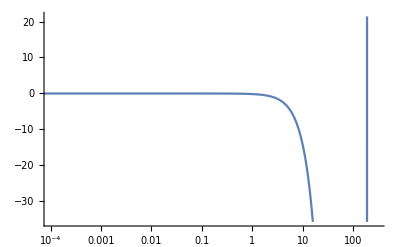

```mathematica
LogLinearPlot[ss2PolSets[[1]],{Subscript[x, 1],0.00001,210},PlotRange->{{0.0001,300},Automatic}]
```

```mathematica
ss3PolSets[[1]]
```

-40565.3+933070. x_1-185031. x_1^2+2618.51 x_1^3-0.0376822 x_1^4+0.00224376 x_1^5

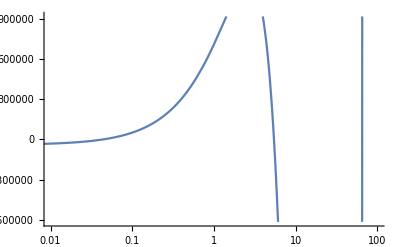

```mathematica
LogLinearPlot[ss3PolSets[[1]],{Subscript[x, 1],0.00001,100},PlotRange->{{0.01,100},Automatic}]
```

## Test

```mathematica
pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.0001])],3]]*1000;
```

```mathematica
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]}
```

{k_1→0.0050108,k_2→2.13937×10^-8,k_3→84.0533,k_4→7.39693×10^-13,k_5→7.02824×10^-6,k_6→2.01154,k_7→0.00200499,k_8→139.788,k_9→277.28,k_10→0.00189982,k_11→3.95171×10^-14,k_12→24.1445,k_13→0.000961332,T_1→4.6296×10^-6,T_2→42.1547,T_3→6.50074×10^-12}

```mathematica
term=coeff1/.subs
```

1.86014×10^-7

```mathematica
term>0
```

True

```mathematica
Solve[pol==0/.subs,Subscript[x, 1]]
```

{{x_1→-69720.},{x_1→-42.1556},{x_1→-0.00140262},{x_1→-1.42528×10^-16},{x_1→2.79523×10^-17}}

```mathematica
pars
```

{109.979,245.987,0.013013,7.38085,0.00907035,0.000240539,8.2791×10^-7,0.0793657,50.8438,0.0447688,0.392116,0.183181,29.0273}

```mathematica
-Log[0.001]
```

6.90776

```mathematica
-Log[1000.]
```

-6.90776

```mathematica
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]]
```

{0.00213335,0.0915725,7.60916,0.0594866,0.0724152,0.44353,0.0398721,0.266627,0.224569,0.04846,1.81477,0.0932097,0.00389391}

```mathematica
pars=Exp[RandomVariate[NormalDistribution[0,Log[1000.]],13]]
```

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

```mathematica
tots=RandomReal[{1,1.*10^4},3]/10^3
```

{9.15425,7.43704,8.1277}

```mathematica
tots=Exp[RandomReal[{Log[0.001],Log[10.]},3]]
```

{0.00214497,1.49576,0.144091}

```mathematica
solution=NSolve[{pol==0}/.subs,Subscript[x, 1]]
```

{{x_1→-0.13976},{x_1→-0.0570779-0.19538 ⅈ},{x_1→-0.0570779+0.19538 ⅈ},{x_1→-0.000112664},{x_1→0.0540014}}

```mathematica
solution=NSolve[{pol==0&&Subscript[x, 1]>0}/.subs,Subscript[x, 1],Reals]
```

{{x_1→0.0540014}}

```mathematica
x=1
x++
```

```mathematica
a=1;
```

```mathematica
b=Switch[a,1,++a,4,a]
```

2